```mathematica
Tau=2Pi;
dBesselI=Derivative[0,1][BesselI];
dBesselJ=Derivative[0,1][BesselJ];dBesselK=Derivative[0,1][BesselK];
dBesselY=Derivative[0,1][BesselY];
exact[{r1_,r2_}]:=Block[{
dI=D[BesselI[#1,x],x]/.{x->#2}&,
dK=D[BesselK[#1,x],x]/.{x-> #2}&,
n0=Ceiling[Log[0.01]/(2 Log[r1/r2])]
},
1/Tau Sum[NIntegrate[Log[1-(dI[k,y r1] dK[k,y r2])/(dI[k, y r2] dK[k,y r1])],{y,0,Infinity}],{k,0,n0}]
];
exactDirichelet[{r1_,r2_}]:=Block[{
n0=Ceiling[Log[0.01]/Log[r1/r2]]
},
1/Tau Sum[NIntegrate[Log[1 - (BesselI[m,y r1] BesselK[m,y r2])/(BesselI[m,y r2] BesselK[m,y r1])], {y, 0, Infinity}], {m, 0, n0}]
];
```

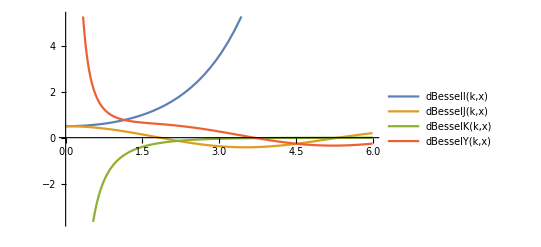

```mathematica
Block[{k=1},
Plot[{dBesselI[k,x],dBesselJ[k,x],dBesselK[k,x],dBesselY[k,x]},{x,0,6},PlotLegends->"Expressions"]
]
```

```mathematica
Db[1,1,20,0.01,0.1][1,10]//AbsoluteTiming
```

-Graphics3D-

{6.29822,{-0.20987,-0.217348,-0.23061,-0.250979,-0.280796,-0.324204,-0.389118,-0.493283,-0.692439,-1.77924,-0.692439,-0.493283,-0.389118,-0.324204,-0.280796,-0.250978,-0.23061,-0.217348,-0.209853,-0.207444}}

```mathematica
ListLinePlot[Db[1,1,30,0.01,0.01][1,10],PlotRange->All]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/4 (1-√5)+1/4 (-1+√5).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/4 (-1-√5)+1/4 (1+√5).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/4 (1-√5)+1/4 (-1+√5).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/4 (-1-√5)+1/4 (1+√5).

$Aborted

-Graphics3D-

{-0.210352,-0.217854,-0.231127,-0.251508,-0.281336,-0.324745,-0.38964,-0.493755,-0.692876,-1.77967,-0.692876,-0.493755,-0.38964,-0.324745,-0.281336,-0.251508,-0.231127,-0.217854,-0.210352,-0.207924}

```mathematica
Db[r_,w_,n_,ϵ_,η_:0.01][β_,j_]:=Module[{s,normal,x,e,d0, M, v},
s[k_]:=(k-1/2)/n;
normal[k_]:=If[β==1,1,-1] *{Cos[Tau s[k]], Sin[Tau s[k]]};
x[t_]:=r*{Cos[Tau  t], Sin[Tau t]};
v=Table[-1/Tau BesselK[0,w Norm[x[s[i]]-(x[s[j]]+ϵ normal[j])]], {i,1,n}];
e[i_,k_]:=If[Abs[i-k]/n≤η,
w r NIntegrate[BesselK[1,w Norm[x[t]-x[s[i]]]] normal[i] . Normalize[x[t]-x[s[i]]],{t,(k-1)/n, k/n}],
w r/n BesselK[1,w Norm[x[s[k]] - x[s[i]]]] normal[i] . Normalize[x[s[k]]-x[s[i]]]//N[#,10]&
];

M=ParallelTable[e[i,k],{i,1,n},{k,1,n}]+1/2 IdentityMatrix[n];
LinearSolve[M,v]
];

source[r_,w_,n_,ϵ_][α_,β_][j_]:=If[α==β,Table[0,n],
Module[{s,normal,x,d0,e,db},
s[k_]:=(k-1/2)/n;
normal[γ_,k_]:=If[γ==1,1,-1] *{Cos[Tau s[k]], Sin[Tau s[k]]};
x[γ_,t_]:=r[[γ]]*{Cos[Tau  t], Sin[Tau t]};
d0=Table[-1/Tau BesselK[0,w Norm[x[α,s[i]]-x[β,s[j]]]],{i,1,n}]//N;
db=Db[r[[β]],w,n,ϵ][β,j];
e=Table[r[[β]]w/n BesselK[1,w Norm[x[β,k]-x[α,i]]] normal[α,i] . Normalize[x[β,k]-x[α,i]],{k,1,n},{i,1,n}];
d0+e . db
]];
concentricCoefficients[rs_,ϵ_][w_][n_][α_,β_][i_,j_]:=
Module[{s,x,normal,d},
s[k_]:=(k-1/2)/n;
normal[γ_,k_]:=If[γ==1,1,-1]{Cos[Tau s[k]], Sin[Tau s[k]]};
x[γ_,k_]:=rs[[γ]] {Cos[Tau s[k]], Sin[Tau s[k]]};
d=x[α,i]-(x[β,j]+ϵ normal[β,j]);
w/Tau  BesselK[1, w Norm[d]](normal[β,j] . Normalize[d])
];

coefficientMatrix[r_,w_,n_,ϵ_]:=ParallelTable[Table[concentricCoefficients[r,ϵ][w][n][α,β][i,j],{i,1,n},{j,1,n}],{α,1,2},{β,1,2}]//ArrayFlatten;

PressureMatrix[r_,w_,n_,ϵ_]:=Module[{M,v},
Print["Generating coefficients..."];
M=coefficientMatrix[r,w,n,ϵ];
Print["Generating source..."];
v=Monitor[Table[ParallelTable[source[r,w,n,ϵ][α,β][j],{j,1,n}],{α,1,2},{β,1,2}],
ProgressIndicator[2(α-1)+(β-1),{0,4}]
]//ArrayFlatten;
LinearSolve[M,v]
];

PressureVector[r_,w_,n_,ϵ_][β_]:=Module[{m,M,v,p},
m=Floor[n/2];
M=coefficientMatrix[r,w,n,ϵ];
v=Join[source[r,w,n,ϵ][1,β][m], source[r,w,n,ϵ][2,β][m]];
p=LinearSolve[M,v];
Table[p[[k]],{k,1,n}]
];

PressurePoint[r_,w_,n_,ϵ_,β_]:=PressureVector[r,w,n,ϵ][β]//Middle;
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«5 more identical outputs»

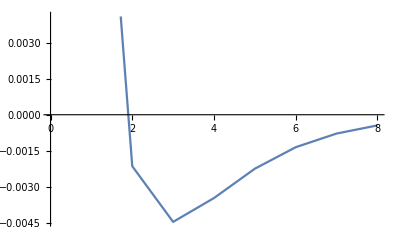

```mathematica
pts=Monitor[Table[PressurePoint[{1,2},w,20,0.1,1],{w,0.25,2,0.25}],ProgressIndicator[w,{0,2}]];
ListLinePlot[pts]
```

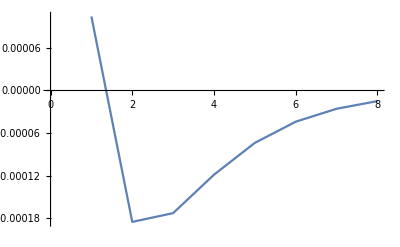

```mathematica
pts//ListLinePlot
```

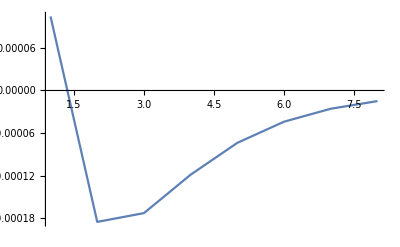

```mathematica
ListLinePlot[pts,PlotRange->All]
```

```mathematica
sourceMatrix[{1,2},1,5,0.1]
```

{{0,0,0,0,0,-0.19774,-0.150247,-0.137162,-0.137162,-0.150247},{0,0,0,0,0,0.0304207,-0.0170728,0.0304207,0.043506,0.043506},{0,0,0,0,0,0.155165,0.142079,0.0945859,0.142079,0.155165},{0,0,0,0,0,0.043506,0.043506,0.0304207,-0.0170728,0.0304207},{0,0,0,0,0,-0.150247,-0.137162,-0.137162,-0.150247,-0.19774},{-0.155352,-0.107858,-0.0947731,-0.0947731,-0.107858,0,0,0,0,0},{0.0142298,-0.0332638,0.0142298,0.027315,0.027315,0,0,0,0,0},{0.10277,0.0896844,0.0421908,0.0896844,0.10277,0,0,0,0,0},{0.027315,0.027315,0.0142298,-0.0332638,0.0142298,0,0,0,0,0},{-0.107858,-0.0947731,-0.0947731,-0.107858,-0.155352,0,0,0,0,0}}

```mathematica
%//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | -0.19774 | -0.150247 | -0.137162 | -0.137162 | -0.150247
0 | 0 | 0 | 0 | 0 | 0.0304207 | -0.0170728 | 0.0304207 | 0.043506 | 0.043506
0 | 0 | 0 | 0 | 0 | 0.155165 | 0.142079 | 0.0945859 | 0.142079 | 0.155165
0 | 0 | 0 | 0 | 0 | 0.043506 | 0.043506 | 0.0304207 | -0.0170728 | 0.0304207
0 | 0 | 0 | 0 | 0 | -0.150247 | -0.137162 | -0.137162 | -0.150247 | -0.19774
-0.155352 | -0.107858 | -0.0947731 | -0.0947731 | -0.107858 | 0 | 0 | 0 | 0 | 0
0.0142298 | -0.0332638 | 0.0142298 | 0.027315 | 0.027315 | 0 | 0 | 0 | 0 | 0
0.10277 | 0.0896844 | 0.0421908 | 0.0896844 | 0.10277 | 0 | 0 | 0 | 0 | 0
0.027315 | 0.027315 | 0.0142298 | -0.0332638 | 0.0142298 | 0 | 0 | 0 | 0 | 0
-0.107858 | -0.0947731 | -0.0947731 | -0.107858 | -0.155352 | 0 | 0 | 0 | 0 | 0)